# 实验习题3

## 工科数学分析——数学实验

## 题1

```mathematica
Manipulate[Plot[Sin[c x],{x,-6,6},PlotRange->{-1.5,1.5}],{c,1,5,0.1}
]
```

## 题2

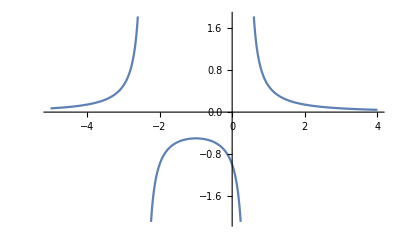

```mathematica
clear[x,c];
f[x_,c_]:=1/(x^2+2 x+c);

Plot[f[x,-1],{x,-5,4},PlotRange->Automatic]
```

观察可得其极大值点为-1，驻点为-1，单调减区间为（-1，-1+√2）和（-1+√2，4），单调增区间为（-5，-1-√2）和（-1-√2，-1），
其图像为凹的区间为(-5，-1-√2)和（-1+√2，4），其图像为凸的区间为(-1-√2，-1+√2)，
其铅直渐进线为x=-1+√2，x=-1-√2，其水平渐进线为y=0。

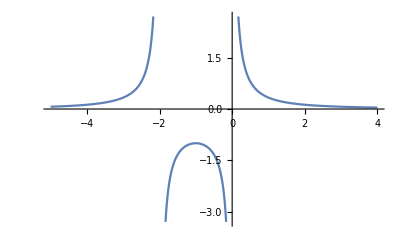

```mathematica
Plot[f[x,0],{x,-5,4},PlotRange->Automatic]
```

观察可得其极大值点为 - 1，驻点为 - 1，单调减区间为 （-1，0） 和 （0，4），单调增区间为 （-2，0） 和 （-5，-2），
 其图像为凹的区间为 (-5，-2) 和 （0，4），其图像为凸的区间为 (-2，0)，
 其铅直渐进线为x = -2，x = 0 ，其水平渐进线为y = 0。

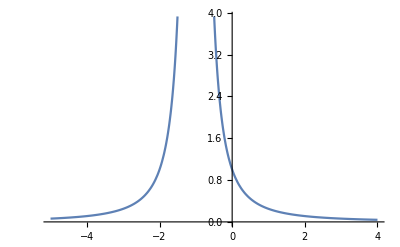

```mathematica
Plot[f[x,1],{x,-5,4},PlotRange->Automatic]
```

观察可得其无极值点，无驻点，单调减区间为 （-1，4），单调增区间为 （-5，-1），
  其图像为凹的区间为 (-5，-1) 和 （-1，4），无图像为凸的区间，
  其铅直渐进线为x = -1，其水平渐进线为y = 0。

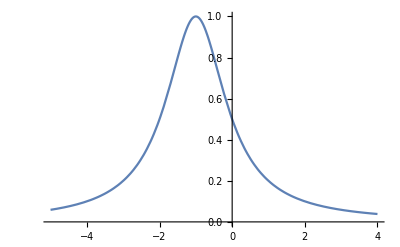

```mathematica
Plot[f[x,2],{x,-5,4},PlotRange->Automatic]
```

观察可得其极大值点为 - 1，驻点为 - 1，单调减区间为 （-1，4），单调增区间为 （-5，-1），
  其图像为凹的区间为 (-5，1/3 (-3-√3)) 和 （1/3 (-3+√3)，4），其图像为凸的区间为 (1/3 (-3-√3)，1/3 (-3+√3))，
  其水平渐进线为y = 0。

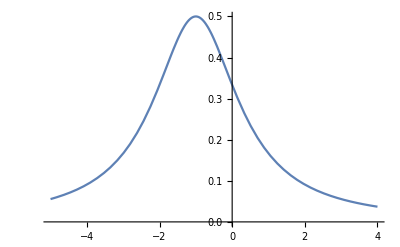

```mathematica
Plot[f[x,3],{x,-5,4},PlotRange->Automatic]
```

观察可得其极大值点为 - 1，驻点为 - 1，单调减区间为 （-1，4），单调增区间为 （-5，-1），
  其图像为凹的区间为 (-5，1/3 (-3-√6)) 和 （1/3 (-3+√6)，4），其图像为凸的区间为 (1/3 (-3-√6)，1/3 (-3+√6))，
  其水平渐进线为y = 0。